# Figures of Efficient Computations of Interesting Paths

## Chapter 1, TDA

```mathematica
Table[{p,{0.4,}}]
```

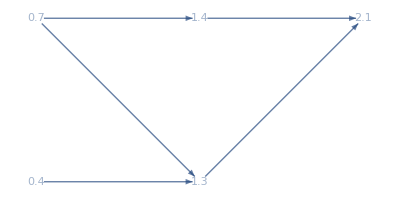

```mathematica
Graph[{0.4,1.3,0.7,1.4,2.1},{0.4->1.3,0.7->1.3,0.7->1.4,1.3->2.1,1.4->2.1},VertexCoordinates->{{0,0},{1,0},{0,1},{1,1},{2,1}},VertexShapeFunction->"Name"]
```

```mathematica
Graph[{0.4,1.3,0.7,1.4,2.1},{0.4->1.3,0.7->1.3,1.3->0.7,0.7->1.4,1.4->0.7,1.3->2.1,1.4->2.1,2.1->1.4},VertexCoordinates->{{0,0},{1,0},{0,1},{1,1},{2,1}},VertexShapeFunction->"Name"]
```

-Graphics-

```mathematica
Graph[{0.4,1.3,0.7,1.4,2.1},{0.4->1.3,1.3->0.4,2.1->1.3,0.7->1.3,1.3->0.7,0.7->1.4,1.4->0.7,1.3->2.1,1.4->2.1,2.1->1.4},VertexCoordinates->{{0,0},{1,0},{0,1},{1,1},{2,1}},VertexShapeFunction->"Name"]
```

-Graphics-

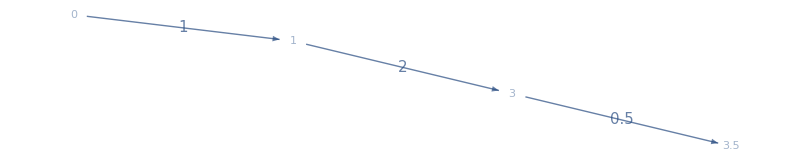

```mathematica
Graph[{0,1,3,3.5},{0->1,1->3,3->3.5},VertexShapeFunction->"Name",EdgeLabels->{0->1->1,1->3->2,3->3.5->0.5},EdgeLabelStyle->Directive[15]]
```

```mathematica
data2D={{83.43,71.19},{6.51,32.82},{45.58,49.94},{55.30,11.22},{10.92,87.52},{4.79,99.65},{75.12,30.42},{33.17,15.32},{86.42,52.07},{66.17,86.34},{95.16,54.78},{11.11,54.48},{26.40,90.55},{15.21,70.46},{54.49,53.07},{15.59,75.91},{42.4,39.57},{32.75,86.89},{13.32,27.02},{39.58,41.69}};
```

```mathematica
data3D={{59.21,47.32,32.91},{91.94,38.30,98.55},{14.09,34.84,69.92},{17.89,96.71,91.15},{64.46,54.30,53.04},{90.93,61.59,34.45},{10.33,57.13,25.61},{18.81,65.06,77.75},{62.79,35.6,9.91},{1.40,4.04,76.18},{30.35,17.40,79.28},{64.35,46.9,85.87},{29.12,31.82,14.14},{83.10,26.77,36.57},{49.56,83.73,5.01},{76.43,13.88,7.3},{41.99,39.7,51.33},{34.77,97.26,62.27},{44.44,29.32,77.85},{46.63,59.30,69.44}};
```

```mathematica
Animate[Graphics3D[Table[Sphere[p,r],{p,data3D}]],{r,0,100}]
```

```mathematica
Animate[Graphics3D[Table[Sphere[p,r],{p,data3D}]],{r,0,100},AnimationRate->5,AnimationDirection->ForwardBackward]
```

Values of r shown: 15 & 20

```mathematica
Graphics3D[Table[Sphere[p,r],{p,data3D}]]
```

```mathematica
Graphics3D[Join[Table[Point[p],{p,data3D}],Table[Simplex[l],{l,Select[Flatten[Table[{p1,p2},{p1,data3D},{p2,data3D}],1],EuclideanDistance[#[[1]],#[[2]]]<=2r&]}],Table[Simplex[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data3D},{p2,data3D},{p3,data3D}],2],EuclideanDistance[#[[1]],#[[2]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&]}]]//Evaluate]
```

```mathematica
Animate[Graphics3D[Join[{Opacity[0.1]},Table[Point[p],{p,data3D}],Table[Simplex[l],{l,Select[Flatten[Table[{p1,p2},{p1,data3D},{p2,data3D}],1],EuclideanDistance[#[[1]],#[[2]]]<=r&]}],Table[Simplex[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data3D},{p2,data3D},{p3,data3D}],2],EuclideanDistance[#[[1]],#[[2]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&]}]]//Evaluate],{r,15,70}]
```

```mathematica
Animate[Graphics3D[Join[{Opacity[0.1]},Table[Point[p],{p,data3D}],Table[Simplex[l],{l,Select[Flatten[Table[{p1,p2},{p1,data3D},{p2,data3D}],1],EuclideanDistance[#[[1]],#[[2]]]<=r&]}],Table[Simplex[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data3D},{p2,data3D},{p3,data3D}],2],EuclideanDistance[#[[1]],#[[2]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&]}]]//Evaluate],{r,15,70},AnimationRate->5,AnimationDirection->ForwardBackward]
```

```mathematica
Animate[Graphics[Evaluate[Join[{Opacity[0.1]},Table[Disk[p,r],{p,data2D}]]]],{r,0,100}]
```

```mathematica
Animate[Graphics[Evaluate[Join[{Opacity[0.1]},Table[Disk[p,r],{p,data2D}]]]],{r,0,100},AnimationRate->5,AnimationDirection->ForwardBackward]
```

```mathematica
Graphics[Evaluate[Join[{Opacity[0.2]},Table[Disk[p,r],{p,data2D}]]]]
```

```mathematica
Animate[Graphics[Join[{Opacity[0.05]},Table[Point[p],{p,data2D}],Table[Line[l],{l,Select[Flatten[Table[{p1,p2},{p1,data2D},{p2,data2D}],1],EuclideanDistance[#[[1]],#[[2]]]<=r&]}],Table[Triangle[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data2D},{p2,data2D},{p3,data2D}],2],EuclideanDistance[#[[1]],#[[2]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&&EuclideanDistance[#[[1]],#[[3]]]<=r&]}]]//Evaluate],{r,0,50},AnimationRate->5,AnimationDirection->ForwardBackward]
```

```mathematica
Graphics[Join[{Opacity[0.2]},Table[Point[p],{p,data2D}],Table[Line[l],{l,Select[Flatten[Table[{p1,p2},{p1,data2D},{p2,data2D}],1],EuclideanDistance[#[[1]],#[[2]]]<=2r&]}],Table[Triangle[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data2D},{p2,data2D},{p3,data2D}],2],EuclideanDistance[#[[1]],#[[2]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&]}]]//Evaluate]]
```

```mathematica
Manipulate[{Graphics[Join[{Opacity[0.05]},Table[Point[p],{p,data2D}],Table[Line[l],{l,Select[Flatten[Table[{p1,p2},{p1,data2D},{p2,data2D}],1],EuclideanDistance[#[[1]],#[[2]]]<=2r&]}],Table[Triangle[t],{t,Select[Flatten[Table[{p1,p2,p3},{p1,data2D},{p2,data2D},{p3,data2D}],2],EuclideanDistance[#[[1]],#[[2]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&&EuclideanDistance[#[[1]],#[[3]]]<=2r&]}]]//Evaluate],Graphics[Evaluate[Join[{Opacity[0.1]},Table[Disk[p,r],{p,data2D}]]]]},{r,0,50},SaveDefinitions->True]
```

## Chapter 3, Max-IP figures

Isolated bidirected edge:

```mathematica
Graph[Range[6],{1->3,2->4,3->4,4->3,3->5,4->6},VertexCoordinates->{{0,0},{1,-1},{1,0},{2,0},{2,1},{3,0}},VertexShapeFunction->"Name"]
```

-Graphics-

Directed acyclic transformation:

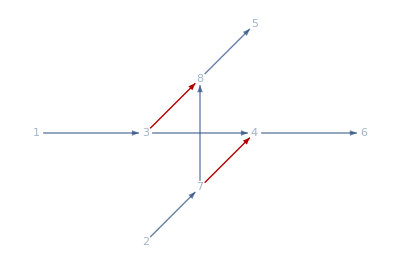

```mathematica
HighlightGraph[Graph[Range[8],{1->3,2->7,7->4,3->4,3->8,4->6,7->8,8->5},VertexCoordinates->{{0,0},{1,-1},{1,0},{2,0},{2,1},{3,0},{1.5,-0.5},{1.5,0.5}},VertexShapeFunction->"Name"],{{7->4,3->8}}]
```

## Chapter 4, 2-IP figures

Initial graph:

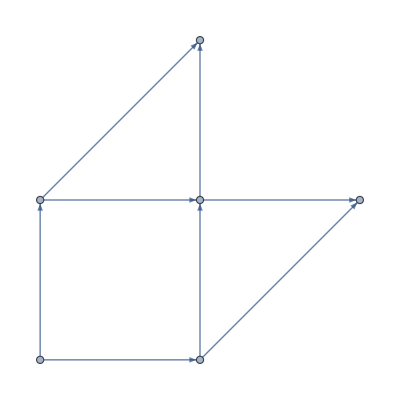

```mathematica
Graph[Range[0,5],{0->1,0->2,1->3,2->3,3->4,1->4,2->5,3->5},VertexCoordinates->{{0,0},{1,0},{0,1},{1,1},{2,1},{1,2}}]
```

Corresponding graph based on edges:

```mathematica
Graph[Join[Range[0,5],{e1,e2,e3,e4,e5,e6,e7,e8}],{0->1,0->2,1->3,2->3,3->4,1->4,2->5,3->5,e1<->e3,e1<->e5,e2<->e4,e2<->e7,e3<->e6,e3<->e8,e4<->e8,e4<->e6},VertexCoordinates->{{0,0},{1,0},{0,1},{1,1},{2,1},{1,2},{0.5,0},{0,0.5},{1,0.5},{0.5,1},{1.5,0.5},{1.5,1},{0.5,1.5},{1,1.5}},EdgeStyle->{e1<->e3->{Hue[0, 1, 0.75],Thick},e1<->e5->{Hue[0, 1, 0.75],Thick},e2<->e4->{Hue[0, 1, 0.75],Thick},e2<->e7->{Hue[0, 1, 0.75],Thick},e3<->e6->{Hue[0, 1, 0.75],Thick},e3<->e8->{Hue[0, 1, 0.75],Thick},e4<->e8->{Hue[0, 1, 0.75],Thick},e4<->e6->{Hue[0, 1, 0.75],Thick}},VertexStyle->{e1->Hue[0, 1, 0.75],e2->Hue[0, 1, 0.75],e3->Hue[0, 1, 0.75],e4->Hue[0, 1, 0.75],e5->Hue[0, 1, 0.75],e6->Hue[0, 1, 0.75],e7->Hue[0, 1, 0.75],e8->Hue[0, 1, 0.75]}]
```

-Graphics-

## Chapter 4, 3-IP proof of NP-completeness

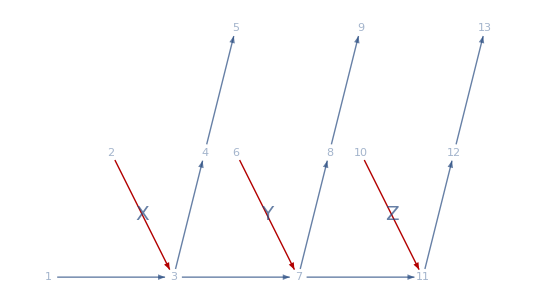

```mathematica
HighlightGraph[Graph[Range[13],{1->3,2->3,3->4,4->5,3->7,6->7,7->8,8->9,7->11,10->11,11->12,12->13},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2}},EdgeLabels->{2->3->Style["X",FontSize->20],6->7->Style["Y",FontSize->20],10->11->Style["Z",FontSize->20]},VertexShapeFunction->"Name"],{2->3,6->7,10->11}]
```

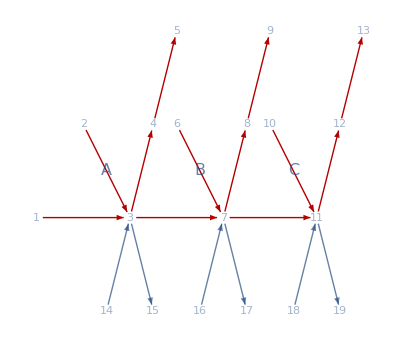

```mathematica
HighlightGraph[Graph[Range[19],{1->3,2->3,3->4,4->5,3->7,6->7,7->8,8->9,7->11,10->11,11->12,12->13,14->3,3->15,16->7,7->17,18->11,11->19},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0.75,-1},{1.25,-1},{1.75,-1},{2.25,-1},{2.75,-1},{3.25,-1}},EdgeLabels->{2->3->Style["A",FontSize->16],6->7->Style["B",FontSize->16],10->11->Style["C",FontSize->16]},VertexShapeFunction->"Name"],{1->3,2->3,3->4,4->5,3->7,6->7,7->8,8->9,7->11,10->11,11->12,12->13}]
```

```mathematica
{0.75,-1},{1.25,-1},{1.75,-1},{2.25,-1},{2.75,-1},{3.25,-1}
```

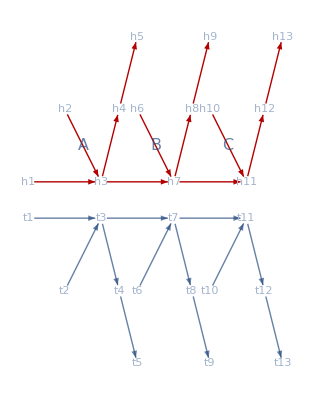

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t6","t7","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h6"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{1.5,-1.5},{2,-0.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h2"->"h3"->Style["A",FontSize->16],"h6"->"h7"->Style["B",FontSize->16],"h10"->"h11"->Style["C",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h6"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

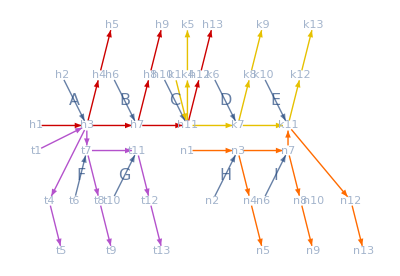

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7","h8","h9","h10","h11","h12","h13","k1","k4","k5","k6","k7","k8","k9","k10","k11","k12","k13","t1","t4","t5","t6","t7","t8","t9","t10","t11","t12","t13","n1","n2","n3","n4","n5","n6","n7","n8","n9","n10","n12","n13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h6"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","k1"->"h11","h11"->"k4","k4"->"k5","h11"->"k7","k6"->"k7","k7"->"k8","k8"->"k9","k7"->"k11","k10"->"k11","k11"->"k12","k12"->"k13","t1"->"h3","h3"->"t4","t4"->"t5","h3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13","n1"->"n3","n2"->"n3","n3"->"n4","n4"->"n5","n3"->"n7","n6"->"n7","n7"->"n8","n8"->"n9","n7"->"k11","k11"->"n12","n12"->"n13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},
{2.75,1},{3,1},{3,2},{3.5,1},{4,0},{4.25,1},{4.5,2},{4.5,1},{5,0},{5.25,1},{5.5,2},
{0,-0.5},{0.25,-1.5},{0.5,-2.5},{0.75,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{1.5,-1.5},{2,-0.5},{2.25,-1.5},{2.5,-2.5},
{3,-0.5},{3.5,-1.5},{4,-0.5},{4.25,-1.5},{4.5,-2.5},{4.5,-1.5},{5,-0.5},{5.25,-1.5},{5.5,-2.5},{5.5,-1.5},{6.25,-1.5},{6.5,-2.5}},EdgeLabels->{"h2"->"h3"->Style["A",FontSize->16],"h6"->"h7"->Style["B",FontSize->16],"h10"->"h11"->Style["C",FontSize->16],"k6"->"k7"->Style["D",FontSize->16],"k10"->"k11"->Style["E",FontSize->16],"t6"->"t7"->Style["F",FontSize->16],"t10"->"t11"->Style["G",FontSize->16],"n2"->"n3"->Style["H",FontSize->16],"n6"->"n7"->Style["I",FontSize->16]},VertexShapeFunction->"Name"],{{"h1"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h11"->"h12","h12"->"h13"},{"k1"->"h11","h11"->"k4","k4"->"k5","h11"->"k7","k7"->"k8","k8"->"k9","k7"->"k11","k11"->"k12","k12"->"k13"},{"t1"->"h3","h3"->"t4","t4"->"t5","h3"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t11"->"t12","t12"->"t13"},{"n1"->"n3","n3"->"n4","n4"->"n5","n3"->"n7","n7"->"n8","n8"->"n9","n7"->"k11","k11"->"n12","n12"->"n13"}}]
```

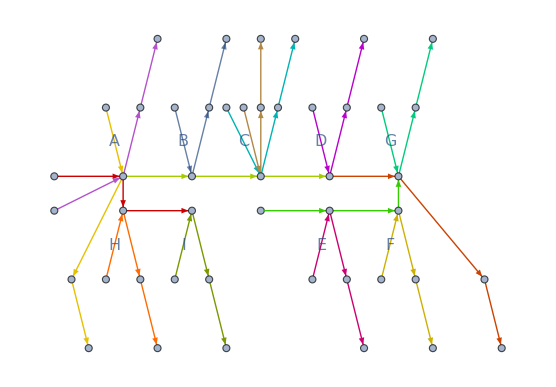

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7","h8","h9","h10","h11","h12","h13","k1","k4","k5","k6","k7","k8","k9","k10","k11","k12","k13","t1","t4","t5","t6","t7","t8","t9","t10","t11","t12","t13","n1","n2","n3","n4","n5","n6","n7","n8","n9","n12","n13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h6"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","k1"->"h11","h11"->"k4","k4"->"k5","h11"->"k7","k6"->"k7","k7"->"k8","k8"->"k9","k7"->"k11","k10"->"k11","k11"->"k12","k12"->"k13","t1"->"h3","h3"->"t4","t4"->"t5","h3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13","n1"->"n3","n2"->"n3","n3"->"n4","n4"->"n5","n3"->"n7","n6"->"n7","n7"->"n8","n8"->"n9","n7"->"k11","k11"->"n12","n12"->"n13"},VertexCoordinates->{{0,0},{0.75,1},{1,0},{1.25,1},{1.5,2},{1.75,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},
{2.75,1},{3,1},{3,2},{3.75,1},{4,0},{4.25,1},{4.5,2},{4.75,1},{5,0},{5.25,1},{5.5,2},
{0,-0.5},{0.25,-1.5},{0.5,-2.5},{0.75,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{1.75,-1.5},{2,-0.5},{2.25,-1.5},{2.5,-2.5},
{3,-0.5},{3.75,-1.5},{4,-0.5},{4.25,-1.5},{4.5,-2.5},{4.75,-1.5},{5,-0.5},{5.25,-1.5},{5.5,-2.5},{6.25,-1.5},{6.5,-2.5}},EdgeLabels->{"h2"->"h3"->Style["A",FontSize->16],"h6"->"h7"->Style["B",FontSize->16],"h10"->"h11"->Style["C",FontSize->16],"k6"->"k7"->Style["D",FontSize->16],"k10"->"k11"->Style["G",FontSize->16],"t6"->"t7"->Style["H",FontSize->16],"t10"->"t11"->Style["I",FontSize->16],"n2"->"n3"->Style["E",FontSize->16],"n6"->"n7"->Style["F",FontSize->16]}],{{"h1"->"h3","h3"->"t7","t7"->"t11"},{"h2"->"h3","h3"->"t4","t4"->"t5"},{"t1"->"h3","h3"->"h4","h4"->"h5"},{"t6"->"t7","t7"->"t8","t8"->"t9"},{"t10"->"t11","t11"->"t12","t12"->"t13"},{"k1"->"h11","h11"->"k4","k4"->"k5"},{"h10"->"h11","h11"->"h12","h12"->"h13"},{"h3"->"h7","h7"->"h11","h11"->"k7"},{"k6"->"k7","k7"->"k8","k8"->"k9"},{"k10"->"k11","k11"->"k12","k12"->"k13"},{"k7"->"k11","k11"->"n12","n12"->"n13"},{"n1"->"n3","n3"->"n7","n7"->"k11"},{"n2"->"n3","n3"->"n4","n4"->"n5"},{"n6"->"n7","n7"->"n8","n8"->"n9"}}]
```

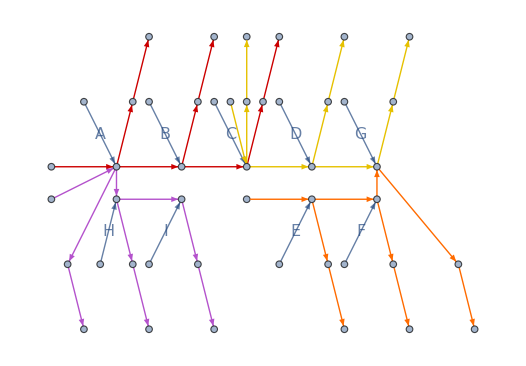

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7","h8","h9","h10","h11","h12","h13","k1","k4","k5","k6","k7","k8","k9","k10","k11","k12","k13","t1","t4","t5","t6","t7","t8","t9","t10","t11","t12","t13","n1","n2","n3","n4","n5","n6","n7","n8","n9","n12","n13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h6"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","k1"->"h11","h11"->"k4","k4"->"k5","h11"->"k7","k6"->"k7","k7"->"k8","k8"->"k9","k7"->"k11","k10"->"k11","k11"->"k12","k12"->"k13","t1"->"h3","h3"->"t4","t4"->"t5","h3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13","n1"->"n3","n2"->"n3","n3"->"n4","n4"->"n5","n3"->"n7","n6"->"n7","n7"->"n8","n8"->"n9","n7"->"k11","k11"->"n12","n12"->"n13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},
{2.75,1},{3,1},{3,2},{3.5,1},{4,0},{4.25,1},{4.5,2},{4.5,1},{5,0},{5.25,1},{5.5,2},
{0,-0.5},{0.25,-1.5},{0.5,-2.5},{0.75,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{1.5,-1.5},{2,-0.5},{2.25,-1.5},{2.5,-2.5},
{3,-0.5},{3.5,-1.5},{4,-0.5},{4.25,-1.5},{4.5,-2.5},{4.5,-1.5},{5,-0.5},{5.25,-1.5},{5.5,-2.5},{6.25,-1.5},{6.5,-2.5}},EdgeLabels->{"h2"->"h3"->Style["A",FontSize->16],"h6"->"h7"->Style["B",FontSize->16],"h10"->"h11"->Style["C",FontSize->16],"k6"->"k7"->Style["D",FontSize->16],"k10"->"k11"->Style["G",FontSize->16],"t6"->"t7"->Style["H",FontSize->16],"t10"->"t11"->Style["I",FontSize->16],"n2"->"n3"->Style["E",FontSize->16],"n6"->"n7"->Style["F",FontSize->16]}],{{"h1"->"h3","h3"->"h4","h4"->"h5","h3"->"h7","h7"->"h8","h8"->"h9","h7"->"h11","h11"->"h12","h12"->"h13"},{"k1"->"h11","h11"->"k4","k4"->"k5","h11"->"k7","k7"->"k8","k8"->"k9","k7"->"k11","k11"->"k12","k12"->"k13"},{"t1"->"h3","h3"->"t4","t4"->"t5","h3"->"t7","t7"->"t8","t8"->"t9","t7"->"t11","t11"->"t12","t12"->"t13"},{"n1"->"n3","n3"->"n4","n4"->"n5","n3"->"n7","n7"->"n8","n8"->"n9","n7"->"k11","k11"->"n12","n12"->"n13"}}]
```

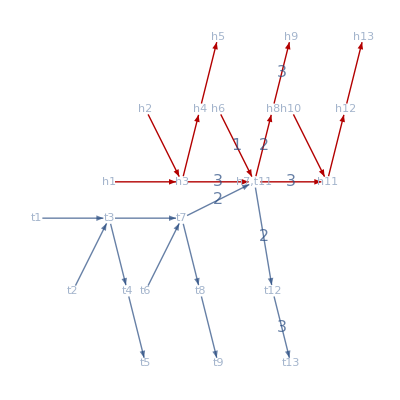

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7,t11","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t6","t7","t8","t9","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t11","h6"->"h7,t11","h7,t11"->"h8","h8"->"h9","h7,t11"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"h7,t11","h7,t11"->"t12","t12"->"t13"},VertexCoordinates->{
{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{-1,-0.5},{-0.5,-1.5},{0,-0.5},{0.25,-1.5},{0.5,-2.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5}},EdgeLabels->{"h6"->"h7,t11"->Style["1",FontSize->16],"h7,t11"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"h7,t11"->"t12"->Style["2",FontSize->16],"t12"->"t13"->Style["3",FontSize->16],"t7"->"h7,t11"->Style["2",FontSize->16],"h3"->"h7,t11"->Style["3",FontSize->16],"h7,t11"->"h11"->Style["3",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t11","h6"->"h7,t11","h7,t11"->"h8","h8"->"h9","h7,t11"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6","h7,t11","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t6","t7","t8","t9","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t11","h6"->"h7,t11","h7,t11"->"h8","h8"->"h9","h7,t11"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"t7","t6"->"t7","t7"->"t8","t8"->"t9","t7"->"h7,t11","h7,t11"->"t12","t12"->"t13"},VertexCoordinates->{
{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{-1,-0.5},{-0.5,-1.5},{0,-0.5},{0.25,-1.5},{0.5,-2.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5}},EdgeLabels->{"h6"->"h7,t11"->Style["1",FontSize->16],"h7,t11"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"h7,t11"->"t12"->Style["2",FontSize->16],"t12"->"t13"->Style["3",FontSize->16],"t7"->"h7,t11"->Style["2",FontSize->16],"h3"->"h7,t11"->Style["3",FontSize->16],"h7,t11"->"h11"->Style["3",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t11","h6"->"h7,t11","h7,t11"->"h8","h8"->"h9","h7,t11"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

-Graphics-

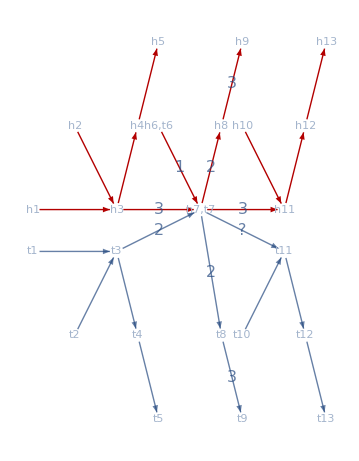

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6,t6","h7,t7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"h7,t7","h7,t7"->"t8","t8"->"t9","h7,t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h7,t7"->"h11"->Style["3",FontSize->16],"h3"->"h7,t7"->Style["3",FontSize->16],"h7,t7"->"t8"->Style["2",FontSize->16],"t8"->"t9"->Style["3",FontSize->16],"h6,t6"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"t3"->"h7,t7"->Style["2",FontSize->16],"h7,t7"->"t11"->Style["?",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

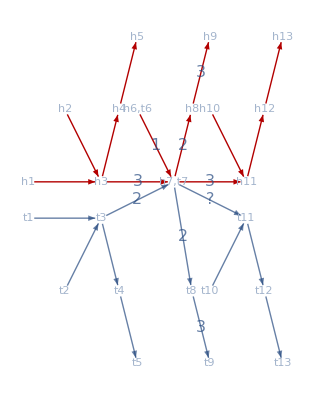

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6,t6","h7,t7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"h7,t7","h7,t7"->"t8","t8"->"t9","h7,t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h7,t7"->"h11"->Style["3",FontSize->16],"h3"->"h7,t7"->Style["3",FontSize->16],"h7,t7"->"t8"->Style["2",FontSize->16],"t8"->"t9"->Style["3",FontSize->16],"h6,t6"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"t3"->"h7,t7"->Style["2",FontSize->16],"h7,t7"->"t11"->Style["?",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6,t6","h7,t7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"h7,t7","h7,t7"->"t8","t8"->"t9","h7,t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h7,t7"->"h11"->Style["3",FontSize->16],"h3"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"t8"->Style["2",FontSize->16],"t8"->"t9"->Style["3",FontSize->16],"h6,t6"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"t3"->"h7,t7"->Style["2",FontSize->16],"h7,t7"->"t11"->Style["?",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

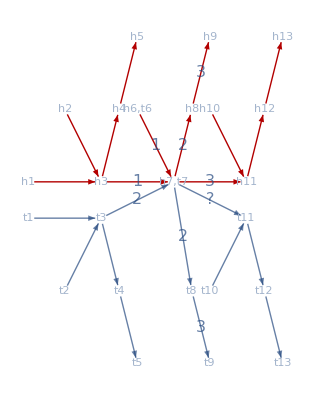

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6,t6","h7,t7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"h7,t7","h7,t7"->"t8","t8"->"t9","h7,t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h7,t7"->"h11"->Style["3",FontSize->16],"h3"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"t8"->Style["2",FontSize->16],"t8"->"t9"->Style["3",FontSize->16],"h6,t6"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"t3"->"h7,t7"->Style["2",FontSize->16],"h7,t7"->"t11"->Style["?",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

```mathematica
HighlightGraph[Graph[{"h1","h2","h3","h4","h5","h6,t6","h7,t7","h8","h9","h10","h11","h12","h13","t1","t2","t3","t4","t5","t8","t9","t10","t11","t12","t13"},{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13","t1"->"t3","t2"->"t3","t3"->"t4","t4"->"t5","t3"->"h7,t7","h7,t7"->"t8","t8"->"t9","h7,t7"->"t11","t10"->"t11","t11"->"t12","t12"->"t13"},VertexCoordinates->{{0,0},{0.5,1},{1,0},{1.25,1},{1.5,2},{1.5,1},{2,0},{2.25,1},{2.5,2},{2.5,1},{3,0},{3.25,1},{3.5,2},{0,-0.5},{0.5,-1.5},{1,-0.5},{1.25,-1.5},{1.5,-2.5},{2.25,-1.5},{2.5,-2.5},{2.5,-1.5},{3,-0.5},{3.25,-1.5},{3.5,-2.5}},EdgeLabels->{"h7,t7"->"h11"->Style["3",FontSize->16],"h3"->"h7,t7"->Style["?",FontSize->16],"h7,t7"->"t8"->Style["2",FontSize->16],"t8"->"t9"->Style["3",FontSize->16],"h6,t6"->"h7,t7"->Style["1",FontSize->16],"h7,t7"->"h8"->Style["2",FontSize->16],"h8"->"h9"->Style["3",FontSize->16],"t3"->"h7,t7"->Style["?",FontSize->16]},VertexShapeFunction->"Name"],{"h1"->"h3","h2"->"h3","h3"->"h4","h4"->"h5","h3"->"h7,t7","h6,t6"->"h7,t7","h7,t7"->"h8","h8"->"h9","h7,t7"->"h11","h10"->"h11","h11"->"h12","h12"->"h13"}]
```

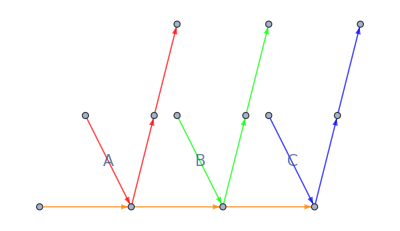

```mathematica
HighlightGraph[Graph[{1->2,2->3,3->4,2->5,5->6,7->2,3->8,8->9,10->3,4->11,11->12,13->4},VertexCoordinates->{{0,0},{1,0},{2,0},{3,0},{1.25,1},{1.5,2},{0.5,1},{2.25,1},{2.5,2},{1.5,1},{3.25,1},{3.5,2},{2.5,1}},EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16]}],{Style[3->8,Green],Style[8->9,Green],Style[2->3,Orange],Style[10->3,Green],Style[2->5,Red],Style[5->6,Red],Style[1->2,Orange],Style[7->2,Red],Style[4->11,Blue],Style[11->12,Blue],Style[3->4,Orange],Style[13->4,Blue]}]
```

```mathematica
{"A","B","C"},{"A","C","D"},{"B","D","F"},{"B","E","F"},{"E","G","H"},{"A","E","I"},{"C","G","H"} 1,{2,4},{3,6,7}
A 7->2 
B 10->3
C 13->4 
D 213->24
E 410->43 
F 313->34
G 510->53 
H 513->54 
I 613->64
```

```mathematica
g1=Graph[{1->2,2->3,3->4,2->5,5->6,7->2,3->8,8->9,10->3,4->11,11->12,13->4}];
g2=Graph[{21->2,2->4,4->24,2->25,25->26,7->2,4->28,28->29,13->4,24->211,211->212,213->24}];
g3=Graph[{31->3,3->24,24->34,3->35,35->36,10->3,24->38,38->39,213->24,34->311,311->312,313->34}];
g4=Graph[{41->3,3->43,43->34,3->45,45->46,10->3,43->48,48->49,410->43,34->411,411->412,313->34}];
g5=Graph[{51->43,43->53,53->54,43->55,55->56,410->43,53->58,58->59,510->53,54->511,511->512,513->54}];
g6=Graph[{61->2,2->43,43->64,2->65,65->66,7->2,43->68,68->69,410->43,64->611,611->612,613->64}];
g7=Graph[{71->4,4->53,53->54,4->75,75->76,13->4,53->78,78->79,510->53,54->711,711->712,513->54}];
```

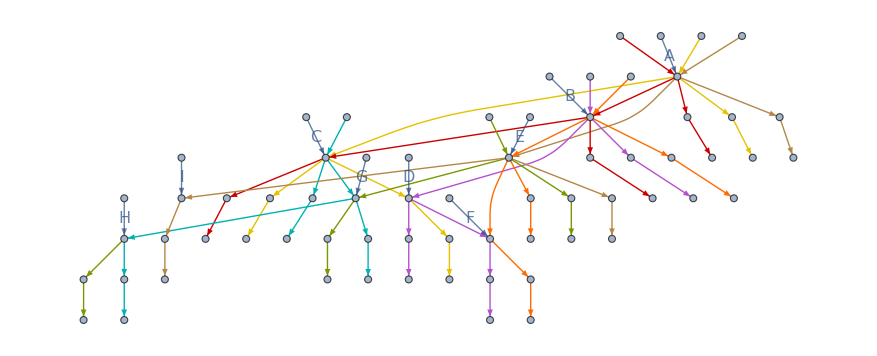

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,g6,g7,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412},
{51->43,43->53,53->54,43->55,55->56,53->58,58->59,54->511,511->512},
{61->2,2->43,43->64,2->65,65->66,43->68,68->69,64->611,611->612},
{71->4,4->53,53->54,4->75,75->76,53->78,78->79,54->711,711->712}
}]
```

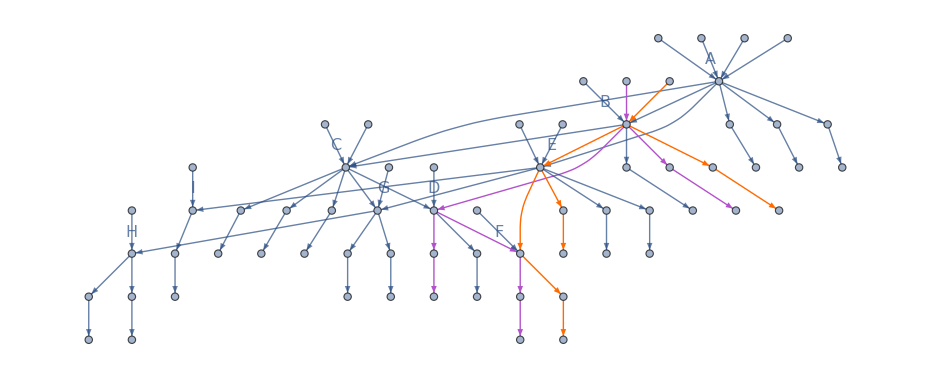

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,g6,g7,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{},{},
{31->3,24->34,3->24,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,3->45,45->46,43->48,48->49,34->411,411->412,43->34},
{},{},{},{}
}]
```

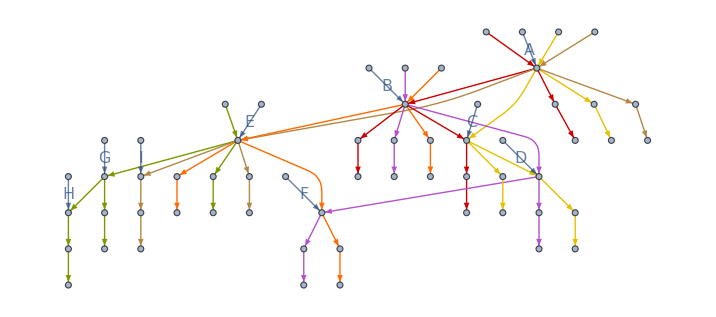

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,g6,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412},
{51->43,43->53,53->54,43->55,55->56,53->58,58->59,54->511,511->512},
{61->2,2->43,43->64,2->65,65->66,43->68,68->69,64->611,611->612}
}]
```

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412},
{51->43,43->53,53->54,43->55,55->56,53->58,58->59,54->511,511->512}
}]
```

-Graphics-

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412}
}]
```

-Graphics-

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312}
}]
```

-Graphics-

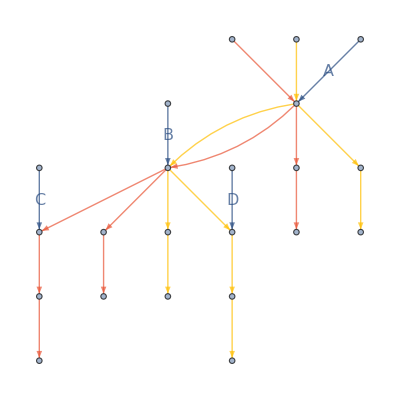

```mathematica
EdgeTaggedGraph[{Style[1->3,RGBColor[0.915, 0.3325, 0.2125]],Style[3->4,RGBColor[0.915, 0.3325, 0.2125]],Style[4->5,RGBColor[0.915, 0.3325, 0.2125]],Style[3->7,RGBColor[0.915, 0.3325, 0.2125]],Style[7->8,RGBColor[0.915, 0.3325, 0.2125]],Style[8->9,RGBColor[0.915, 0.3325, 0.2125]],Style[7->11,RGBColor[0.915, 0.3325, 0.2125]],Style[11->12,RGBColor[0.915, 0.3325, 0.2125]],Style[12->13,RGBColor[0.915, 0.3325, 0.2125]],Style[21->3,RGBColor[1, 0.75, 0]],Style[3->24,RGBColor[1, 0.75, 0]],Style[24->25,RGBColor[1, 0.75, 0]],Style[3->7,RGBColor[1, 0.75, 0]],Style[7->28,RGBColor[1, 0.75, 0]],Style[28->29,RGBColor[1, 0.75, 0]],Style[7->211,RGBColor[1, 0.75, 0]],Style[211->212,RGBColor[1, 0.75, 0]],Style[212->213,RGBColor[1, 0.75, 0]],2->3,6->7,10->11,210->211},EdgeLabels->{2->3->Style["A",FontSize->16],6->7->Style["B",FontSize->16],10->11->Style["C",FontSize->16],210->211->Style["D",FontSize->16]}]
```

```mathematica
HighlightGraph[GraphUnion[g1,g2,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212}
}]
```

-Graphics-

```mathematica
HighlightGraph[GraphUnion[g1,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12}
}]
```

-Graphics-

```mathematica
{2,4},{3,6,7}
```

```mathematica
{"A","B","C"},{"A","C","D"},{"B","D","F"},{"B","E","F"},{"E","G","H"},{"A","E","I"},{"C","G","H"} 1,{2,4},{3,6,7}
A 7->2 
B 10->3
C 13->4 
D 213->24
E 410->43 
F 313->34
G 510->53 
H 513->54 
I 613->64
```

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212,7->2,13->4 ,213->24},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412,10->3,410->43 ,313->34}
}]
```

-Graphics-

```mathematica
{"A","B","C"},{"A","C","D"},{"B","D","F"},{"B","E","F"},{"E","G","H"},{"A","E","I"},{"C","G","H"} 1,{2,4},{3,6,7}
A 7->2 
B 10->3
C 13->4 
D 213->24
E 410->43 
F 313->34
G 510->53
H 513->54 
I 613->64
```

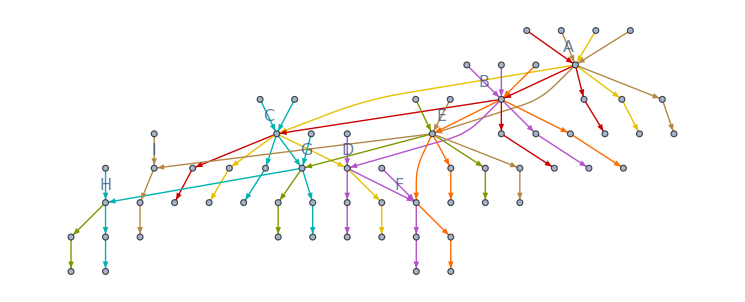

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,g6,g7,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{1->2,2->3,3->4,2->5,5->6,3->8,8->9,4->11,11->12},{21->2,2->4,4->24,2->25,25->26,4->28,28->29,24->211,211->212},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312,213->24,10->3,313->34},
{41->3,3->43,43->34,3->45,45->46,43->48,48->49,34->411,411->412},
{51->43,43->53,53->54,43->55,55->56,53->58,58->59,54->511,511->512},
{61->2,2->43,43->64,2->65,65->66,43->68,68->69,64->611,611->612,410->43 ,7->2 ,613->64},
{71->4,4->53,53->54,4->75,75->76,53->78,78->79,54->711,711->712,510->53 ,13->4 ,513->54}
}]
```

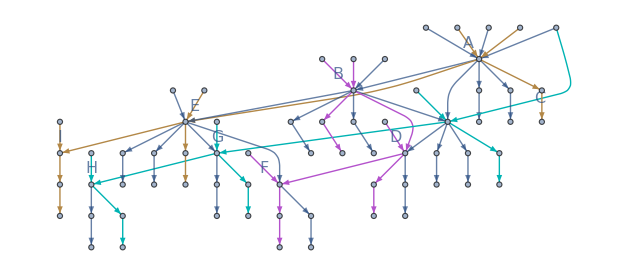

```mathematica
HighlightGraph[GraphUnion[g1,g2,g3,g4,g5,g6,g7,EdgeLabels->{7->2->Style["A",FontSize->16],10->3->Style["B",FontSize->16],13->4->Style["C",FontSize->16],213->24->Style["D",FontSize->16],410->43 ->Style["E",FontSize->16],313->34->Style["F",FontSize->16],510->53 ->Style["G",FontSize->16],513->54 ->Style["H",FontSize->16],613->64->Style["I",FontSize->16]},GraphLayout->"LayeredDigraphEmbedding"],{{},{},
{31->3,3->24,24->34,3->35,35->36,24->38,38->39,34->311,311->312,213->24,10->3,313->34},
{},{},
{61->2,2->43,43->64,2->65,65->66,43->68,68->69,64->611,611->612,410->43 ,7->2 ,613->64},
{71->4,4->53,53->54,4->75,75->76,53->78,78->79,54->711,711->712,510->53 ,13->4 ,513->54}
}]
```

## Chapter 4: k-IP proof of NP-completeness

To generate any graph given a boolean formula (the number is the index of the literal, the sign is the negation of the literal)

```mathematica
b={{1,2,3},{-1,-2,-3},{1,-2,-3}};
```

Figures for the example:

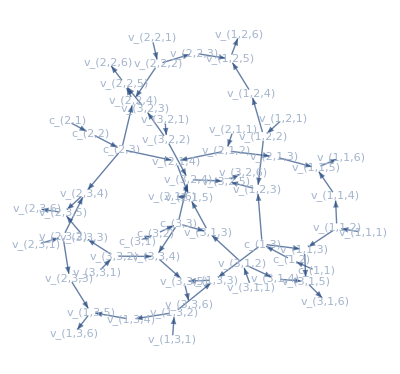

```mathematica
g=Graph[Flatten[Table[
clause=b[[c]];
Join[
{Subscript["c",Sequence[c,1]]->Subscript["c",Sequence[c,2]],Subscript["c",Sequence[c,2]]->Subscript["c",Sequence[c,3]]},
Table[
var=clause[[v]];
varA=Abs[var];
Join[

{Subscript["v",Sequence[c,varA,1]]->Subscript["v",Sequence[c,varA,2]],Subscript["v",Sequence[c,varA,2]]->Subscript["v",Sequence[c,varA,3]],Subscript["v",Sequence[c,varA,3]]->Subscript["v",Sequence[If[Position[Abs[b],varA][[1,1]]==c,Position[Abs[b],varA][[-1,1]],Position[Abs[b],varA][[FirstPosition[Position[Abs[b],varA][[All,1]],c][[1]]-1,1]]],varA,5]],Subscript["v",Sequence[c,varA,2]]->Subscript["v",Sequence[c,varA,4]],Subscript["v",Sequence[c,varA,4]]->Subscript["v",Sequence[c,varA,5]],Subscript["v",Sequence[c,varA,5]]->Subscript["v",Sequence[c,varA,6]]},

{If[Positive[var],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,3]],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,4]]]}
],
{v,Length[clause]}]],
{c,Length[b]}]],VertexShapeFunction->"Name"]
```

```mathematica
b={{1,2},{-1,-2}};
```

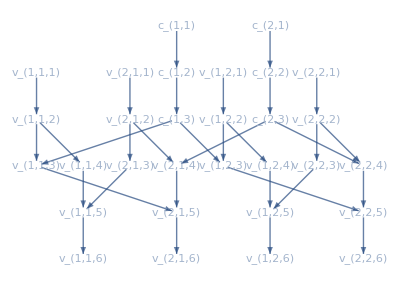

```mathematica
g=Graph[Flatten[{Table[Subscript["v",Sequence[j,x,i]],{x,1,2},{j,1,2},{i,1,6}],Table[Subscript["c",Sequence[x,i]],{x,2},{i,3}]}],Flatten[Table[
clause=b[[c]];
Join[
{Subscript["c",Sequence[c,1]]->Subscript["c",Sequence[c,2]],Subscript["c",Sequence[c,2]]->Subscript["c",Sequence[c,3]]},
Table[
var=clause[[v]];
varA=Abs[var];
Join[

{Subscript["v",Sequence[c,varA,1]]->Subscript["v",Sequence[c,varA,2]],Subscript["v",Sequence[c,varA,2]]->Subscript["v",Sequence[c,varA,3]],Subscript["v",Sequence[c,varA,3]]->Subscript["v",Sequence[If[Position[Abs[b],varA][[1,1]]==c,Position[Abs[b],varA][[-1,1]],Position[Abs[b],varA][[FirstPosition[Position[Abs[b],varA][[All,1]],c][[1]]-1,1]]],varA,5]],Subscript["v",Sequence[c,varA,2]]->Subscript["v",Sequence[c,varA,4]],Subscript["v",Sequence[c,varA,4]]->Subscript["v",Sequence[c,varA,5]],Subscript["v",Sequence[c,varA,5]]->Subscript["v",Sequence[c,varA,6]]},

{If[Positive[var],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,3]],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,4]]]}
],
{v,Length[clause]}]],
{c,Length[b]}]],VertexShapeFunction->"Name",VertexCoordinates->Flatten[{Table[{{0+2i,4},{0+2i,3},{0+2i,2},{1+2i,2},{1+2i,1},{1+2i,0}},{i,0,3}],Table[{2x+3,6-i},{x,0,1},{i,3}]},2]]
```

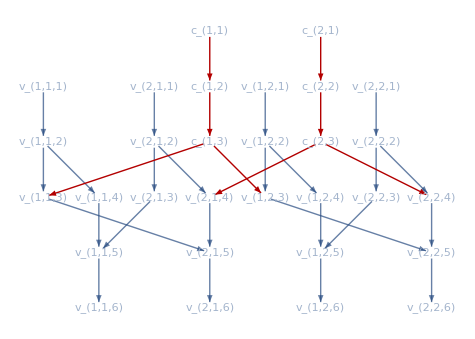

```mathematica
HighlightGraph[g,Flatten[Table[clause=b[[c]];Join[{Subscript["c",Sequence[c,1]]->Subscript["c",Sequence[c,2]],Subscript["c",Sequence[c,2]]->Subscript["c",Sequence[c,3]]},Table[var=clause[[v]];varA=Abs[var];{If[Positive[var],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,3]],Subscript["c",Sequence[c,3]]->Subscript["v",Sequence[c,varA,4]]]},{v,Length[clause]}]],{c,Length[b]}]]]
```

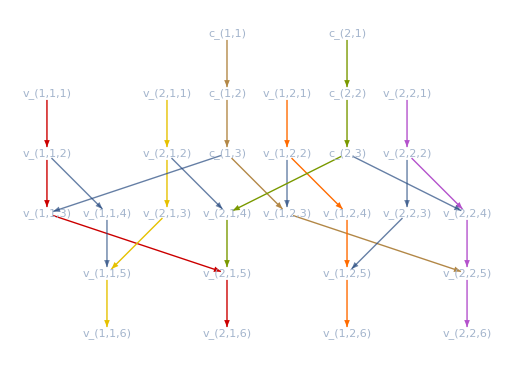

```mathematica
HighlightGraph[g,{{Subscript["v",Sequence[1,1,1]]->Subscript["v",Sequence[1,1,2]],Subscript["v",Sequence[1,1,2]]->Subscript["v",Sequence[1,1,3]],Subscript["v",Sequence[1,1,3]]->Subscript["v",Sequence[2,1,5]],Subscript["v",Sequence[2,1,5]]->Subscript["v",Sequence[2,1,6]]},{Subscript["v",Sequence[2,1,1]]->Subscript["v",Sequence[2,1,2]],Subscript["v",Sequence[2,1,2]]->Subscript["v",Sequence[2,1,3]],Subscript["v",Sequence[2,1,3]]->Subscript["v",Sequence[1,1,5]],Subscript["v",Sequence[1,1,5]]->Subscript["v",Sequence[1,1,6]]},{Subscript["v",Sequence[2,2,1]]->Subscript["v",Sequence[2,2,2]],Subscript["v",Sequence[2,2,2]]->Subscript["v",Sequence[2,2,4]],Subscript["v",Sequence[2,2,4]]->Subscript["v",Sequence[2,2,5]],Subscript["v",Sequence[2,2,5]]->Subscript["v",Sequence[2,2,6]]},{Subscript["v",Sequence[1,2,1]]->Subscript["v",Sequence[1,2,2]],Subscript["v",Sequence[1,2,2]]->Subscript["v",Sequence[1,2,4]],Subscript["v",Sequence[1,2,4]]->Subscript["v",Sequence[1,2,5]],Subscript["v",Sequence[1,2,5]]->Subscript["v",Sequence[1,2,6]]},{Subscript["c",Sequence[2,1]]->Subscript["c",Sequence[2,2]],Subscript["c",Sequence[2,2]]->Subscript["c",Sequence[2,3]],Subscript["c",Sequence[2,3]]->Subscript["v",Sequence[2,1,4]],Subscript["v",Sequence[2,1,4]]->Subscript["v",Sequence[2,1,5]]},{Subscript["c",Sequence[1,1]]->Subscript["c",Sequence[1,2]],Subscript["c",Sequence[1,2]]->Subscript["c",Sequence[1,3]],Subscript["c",Sequence[1,3]]->Subscript["v",Sequence[1,2,3]],Subscript["v",Sequence[1,2,3]]->Subscript["v",Sequence[2,2,5]]}}]
```

```mathematica
Clear[positiveGadget,negativeGadget]
positiveGadget[var_,clause_,m_,i_]:=#[[1]]->#[[2]]&/@Partition[{Subscript[v,Sequence[var,i,1]],Subscript[c,Sequence[clause,3]],Subscript[v,Sequence[var,i,4]],Subscript[v,Sequence[var,i,5]],Subscript[v,Sequence[var,i,6]]},2,1]
negativeGadget[var_,clause_,m_,i_]:=#[[1]]->#[[2]]&/@Partition[{Subscript[v,Sequence[var,i,1]],Subscript[c,Sequence[clause,3]],Subscript[v,Sequence[var,i,3]],Subscript[v,Sequence[var,Mod[i-2,m]+1,5]],Subscript[v,Sequence[var,Mod[i-2,m]+1,6]]},2,1]
positiveGadget[var_,m_,i_]:=#[[1]]->#[[2]]&/@Partition[{Subscript[v,Sequence[var,i,1]],Subscript[v,Sequence[var,i,2]],Subscript[v,Sequence[var,i,4]],Subscript[v,Sequence[var,i,5]],Subscript[v,Sequence[var,i,6]]},2,1]
negativeGadget[var_,m_,i_]:=#[[1]]->#[[2]]&/@Partition[{Subscript[v,Sequence[var,i,1]],Subscript[v,Sequence[var,i,2]],Subscript[v,Sequence[var,i,3]],Subscript[v,Sequence[var,Mod[i-2,m]+1,5]],Subscript[v,Sequence[var,Mod[i-2,m]+1,6]]},2,1]
```

## Chapter 6: IP completeness

```mathematica
Subscript["e","y1,11"]
```

e_(y1,11)

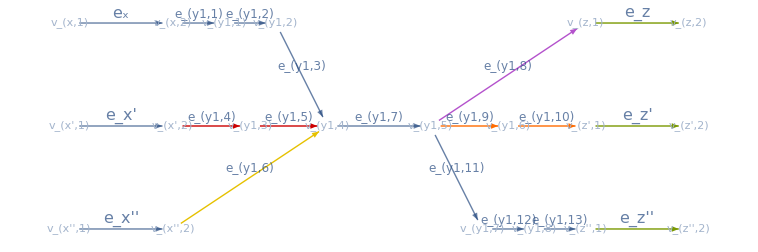

```mathematica
HighlightGraph[Graph[{Subscript["v","x,1"],Subscript["v","x,2"],Subscript["v","y1,1"],Subscript["v","y1,2"],Subscript["v","x',1"],Subscript["v","x',2"],Subscript["v","y1,3"],Subscript["v","x'',1"],Subscript["v","x'',2"],Subscript["v","y1,4"],Subscript["v","y1,5"],Subscript["v","z,1"],Subscript["v","z,2"],Subscript["v","y1,6"],Subscript["v","z',1"],Subscript["v","z',2"],Subscript["v","y1,7"],Subscript["v","y1,8"],Subscript["v","z'',1"],Subscript["v","z'',2"]},{
Subscript["v","x,1"]->Subscript["v","x,2"],Subscript["v","x,2"]->Subscript["v","y1,1"],Subscript["v","y1,1"]->Subscript["v","y1,2"],Subscript["v","y1,2"]->Subscript["v","y1,4"],Subscript["v","y1,4"]->Subscript["v","y1,5"],Subscript["v","y1,5"]->Subscript["v","z,1"],Subscript["v","z,1"]->Subscript["v","z,2"],
Subscript["v","x',1"]->Subscript["v","x',2"],Subscript["v","x',2"]->Subscript["v","y1,3"],Subscript["v","y1,3"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,6"],Subscript["v","y1,6"]->Subscript["v","z',1"],Subscript["v","z',1"]->Subscript["v","z',2"],
Subscript["v","x'',1"]->Subscript["v","x'',2"],Subscript["v","x'',2"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,7"],Subscript["v","y1,7"]->Subscript["v","y1,8"],Subscript["v","y1,8"]->Subscript["v","z'',1"],Subscript["v","z'',1"]->Subscript["v","z'',2"]},VertexCoordinates->{{0,2},{1,2},{1.5,2},{2,2},{0,1},{1,1},{1.75,1},{0,0},{1,0},{2.5,1},{3.5,1},{5,2},{6,2},{4.25,1},{5,1},{6,1},{4,0},{4.5,0},{5,0},{6,0}},VertexShapeFunction->"Name",VertexStyle->Thick,EdgeLabels->{Subscript["v","x,1"]->Subscript["v","x,2"]->Placed[Style[Subscript["e","x"],FontSize->16],1/2],Subscript["v","x',1"]->Subscript["v","x',2"]->Placed[Style[Subscript["e","x'"],FontSize->16],1/2],Subscript["v","x'',1"]->Subscript["v","x'',2"]->Placed[Style[Subscript["e","x''"],FontSize->16],1/2],Subscript["v","z,1"]->Subscript["v","z,2"]->Placed[Style[Subscript["e","z"],FontSize->16],1/2],Subscript["v","z',1"]->Subscript["v","z',2"]->Placed[Style[Subscript["e","z'"],FontSize->16],1/2],Subscript["v","z'',1"]->Subscript["v","z'',2"]->Placed[Style[Subscript["e","z''"],FontSize->16],1/2],
Subscript["v","x,2"]->Subscript["v","y1,1"]->Placed[Style[Subscript["e","y1,1"],FontSize->12],1/2],Subscript["v","y1,1"]->Subscript["v","y1,2"]->Placed[Style[Subscript["e","y1,2"],FontSize->12],1/2],Subscript["v","y1,2"]->Subscript["v","y1,4"]->Placed[Style[Subscript["e","y1,3"],FontSize->12],1/2],Subscript["v","x',2"]->Subscript["v","y1,3"]->Placed[Style[Subscript["e","y1,4"],FontSize->12],1/2],Subscript["v","y1,3"]->Subscript["v","y1,4"]->Placed[Style[Subscript["e","y1,5"],FontSize->12],1/2],Subscript["v","x'',2"]->Subscript["v","y1,4"]->Placed[Style[Subscript["e","y1,6"],FontSize->12],1/2],Subscript["v","y1,4"]->Subscript["v","y1,5"]->Placed[Style[Subscript["e","y1,7"],FontSize->12],1/2],Subscript["v","y1,5"]->Subscript["v","z,1"]->Placed[Style[Subscript["e","y1,8"],FontSize->12],1/2],Subscript["v","y1,5"]->Subscript["v","y1,6"]->Placed[Style[Subscript["e","y1,9"],FontSize->12],1/2],Subscript["v","y1,6"]->Subscript["v","z',1"]->Placed[Style[Subscript["e","y1,10"],FontSize->12],1/2],Subscript["v","y1,5"]->Subscript["v","y1,7"]->Placed[Style[Subscript["e","y1,11"],FontSize->12],1/2],Subscript["v","y1,7"]->Subscript["v","y1,8"]->Placed[Style[Subscript["e","y1,12"],FontSize->12],1/2],Subscript["v","y1,8"]->Subscript["v","z'',1"]->Placed[Style[Subscript["e","y1,13"],FontSize->12],1/2]},BaselinePosition->Axis,ImagePadding->5],{{Subscript["v","x',2"]->Subscript["v","y1,3"],Subscript["v","y1,3"]->Subscript["v","y1,4"]},{Subscript["v","x'',2"]->Subscript["v","y1,4"]},{Subscript["v","y1,5"]->Subscript["v","z,1"]},{Subscript["v","y1,5"]->Subscript["v","y1,6"],Subscript["v","y1,6"]->Subscript["v","z',1"]},{Subscript["v","z,1"]->Subscript["v","z,2"],Subscript["v","z',1"]->Subscript["v","z',2"],Subscript["v","z'',1"]->Subscript["v","z'',2"]}}]
```

```mathematica
{x1,y1,z1},{x2,y1,z2},{x3,y1,z3},
{x1,y2,z1},{x3,y2,z3},{x4,y2,z4}
```

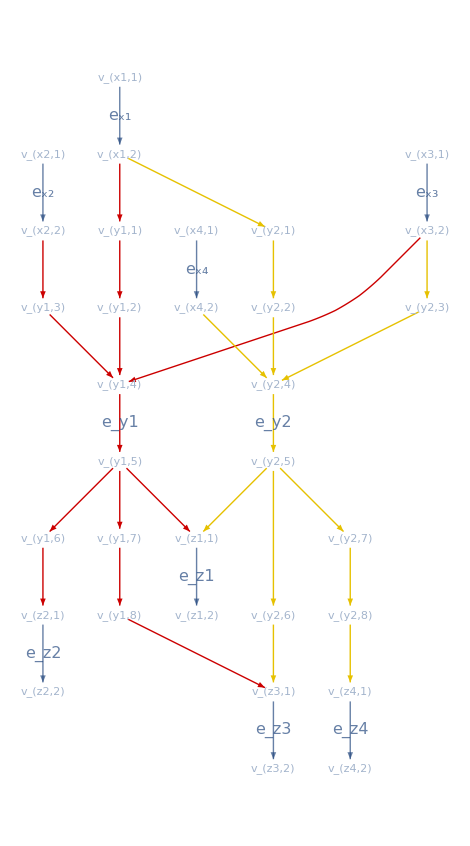

```mathematica
HighlightGraph[Graph[{Subscript["v","x1,1"],Subscript["v","x1,2"],Subscript["v","y1,1"],Subscript["v","y1,2"],Subscript["v","x2,1"],Subscript["v","x2,2"],Subscript["v","y1,3"],Subscript["v","x3,1"],Subscript["v","x3,2"],Subscript["v","y1,4"],Subscript["v","y1,5"],Subscript["v","z1,1"],Subscript["v","z1,2"],Subscript["v","y1,6"],Subscript["v","z2,1"],Subscript["v","z2,2"],Subscript["v","y1,7"],Subscript["v","y1,8"],Subscript["v","z3,1"],Subscript["v","z3,2"],Subscript["v","y2,1"],Subscript["v","y2,2"],Subscript["v","y2,3"],Subscript["v","y2,4"],Subscript["v","y2,5"],Subscript["v","z4,1"],Subscript["v","z4,2"],Subscript["v","y2,6"],Subscript["v","x4,1"],Subscript["v","x4,2"],Subscript["v","y2,7"],Subscript["v","y2,8"]},{
Subscript["v","x1,1"]->Subscript["v","x1,2"],Subscript["v","x1,2"]->Subscript["v","y1,1"],Subscript["v","y1,1"]->Subscript["v","y1,2"],Subscript["v","y1,2"]->Subscript["v","y1,4"],Subscript["v","y1,4"]->Subscript["v","y1,5"],Subscript["v","y1,5"]->Subscript["v","z1,1"],Subscript["v","z1,1"]->Subscript["v","z1,2"],
Subscript["v","x2,1"]->Subscript["v","x2,2"],Subscript["v","x2,2"]->Subscript["v","y1,3"],Subscript["v","y1,3"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,6"],Subscript["v","y1,6"]->Subscript["v","z2,1"],Subscript["v","z2,1"]->Subscript["v","z2,2"],
Subscript["v","x3,1"]->Subscript["v","x3,2"],Subscript["v","x3,2"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,7"],Subscript["v","y1,7"]->Subscript["v","y1,8"],Subscript["v","y1,8"]->Subscript["v","z3,1"],Subscript["v","z3,1"]->Subscript["v","z3,2"],
Subscript["v","x1,2"]->Subscript["v","y2,1"],Subscript["v","y2,1"]->Subscript["v","y2,2"],Subscript["v","y2,2"]->Subscript["v","y2,4"],Subscript["v","y2,4"]->Subscript["v","y2,5"],Subscript["v","y2,5"]->Subscript["v","z1,1"],
Subscript["v","x3,2"]->Subscript["v","y2,3"],Subscript["v","y2,3"]->Subscript["v","y2,4"],Subscript["v","y2,5"]->Subscript["v","y2,6"],Subscript["v","y2,6"]->Subscript["v","z3,1"],
Subscript["v","x4,1"]->Subscript["v","x4,2"],Subscript["v","x4,2"]->Subscript["v","y2,4"],Subscript["v","y2,5"]->Subscript["v","y2,7"],Subscript["v","y2,7"]->Subscript["v","y2,8"],Subscript["v","y2,8"]->Subscript["v","z4,1"],Subscript["v","z4,1"]->Subscript["v","z4,2"]
},VertexShapeFunction->"Name",EdgeLabels->{Subscript["v","x1,1"]->Subscript["v","x1,2"]->Style[Subscript["e","x1"],FontSize->16],Subscript["v","x2,1"]->Subscript["v","x2,2"]->Style[Subscript["e","x2"],FontSize->16],Subscript["v","x3,1"]->Subscript["v","x3,2"]->Style[Subscript["e","x3"],FontSize->16],Subscript["v","x4,1"]->Subscript["v","x4,2"]->Style[Subscript["e","x4"],FontSize->16],Subscript["v","z1,1"]->Subscript["v","z1,2"]->Style[Subscript["e","z1"],FontSize->16],Subscript["v","z2,1"]->Subscript["v","z2,2"]->Style[Subscript["e","z2"],FontSize->16],Subscript["v","z3,1"]->Subscript["v","z3,2"]->Style[Subscript["e","z3"],FontSize->16],Subscript["v","z4,1"]->Subscript["v","z4,2"]->Style[Subscript["e","z4"],FontSize->16],Subscript["v","y1,4"]->Subscript["v","y1,5"]->Style[Subscript["e","y1"],FontSize->16],Subscript["v","y2,4"]->Subscript["v","y2,5"]->Style[Subscript["e","y2"],FontSize->16]}],{{Subscript["v","x1,2"]->Subscript["v","y1,1"],Subscript["v","y1,1"]->Subscript["v","y1,2"],Subscript["v","y1,2"]->Subscript["v","y1,4"],Subscript["v","y1,4"]->Subscript["v","y1,5"],Subscript["v","y1,5"]->Subscript["v","z1,1"],
Subscript["v","x2,2"]->Subscript["v","y1,3"],Subscript["v","y1,3"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,6"],Subscript["v","y1,6"]->Subscript["v","z2,1"],
Subscript["v","x3,2"]->Subscript["v","y1,4"],Subscript["v","y1,5"]->Subscript["v","y1,7"],Subscript["v","y1,7"]->Subscript["v","y1,8"],Subscript["v","y1,8"]->Subscript["v","z3,1"]},{Subscript["v","x1,2"]->Subscript["v","y2,1"],Subscript["v","y2,1"]->Subscript["v","y2,2"],Subscript["v","y2,2"]->Subscript["v","y2,4"],Subscript["v","y2,4"]->Subscript["v","y2,5"],Subscript["v","y2,5"]->Subscript["v","z1,1"],
Subscript["v","x3,2"]->Subscript["v","y2,3"],Subscript["v","y2,3"]->Subscript["v","y2,4"],Subscript["v","y2,5"]->Subscript["v","y2,6"],Subscript["v","y2,6"]->Subscript["v","z3,1"],
Subscript["v","x4,2"]->Subscript["v","y2,4"],Subscript["v","y2,5"]->Subscript["v","y2,7"],Subscript["v","y2,7"]->Subscript["v","y2,8"],Subscript["v","y2,8"]->Subscript["v","z4,1"]}}]
```

Alternative proof of IP completeness

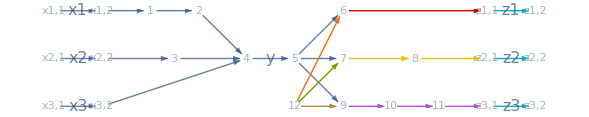

```mathematica
HighlightGraph[Graph[{"x1,1","x1,2","1","2","x2,1","x2,2","3","x3,1","x3,2","4","5","6","z1,1","z1,2","7","8","z2,1","z2,2","y1,9","10","11","z3,1","z3,2","12"},{
"x1,1"->"x1,2","x1,2"->"1","1"->"2","2"->"4","4"->"5","5"->"6","6"->"z1,1","z1,1"->"z1,2",
"x2,1"->"x2,2","x2,2"->"3","3"->"4","5"->"7","7"->"8","8"->"z2,1","z2,1"->"z2,2",
"x3,1"->"x3,2","x3,2"->"4","5"->"y1,9","y1,9"->"10","10"->"11","11"->"z3,1","z3,1"->"z3,2","12"->"6","12"->"7","12"->"y1,9"},VertexCoordinates->{{0,2},{1,2},{2,2},{3,2},{0,1},{1,1},{2.5,1},{0,0},{1,0},{4,1},{5,1},{6,2},{9,2},{10,2},{6,1},{7.5,1},{9,1},{10,1},{6,0},{7,0},{8,0},{9,0},{10,0},{5,0}},VertexShapeFunction->"Name",EdgeLabels->{"x1,1"->"x1,2"->Style["x1",FontSize->16],"x2,1"->"x2,2"->Style["x2",FontSize->16],"x3,1"->"x3,2"->Style["x3",FontSize->16],"z1,1"->"z1,2"->Style["z1",FontSize->16],"z2,1"->"z2,2"->Style["z2",FontSize->16],"z3,1"->"z3,2"->Style["z3",FontSize->16],"4"->"5"->Style["y",FontSize->16]}],{{"6"->"z1,1"},{"7"->"8","8"->"z2,1"},{"y1,9"->"10","10"->"11","11"->"z3,1"},{"12"->"6"},{"12"->"7"},{"12"->"y1,9"},{"z1,1"->"z1,2","z2,1"->"z2,2","z3,1"->"z3,2"}}]
```

```mathematica
HighlightGraph[Graph[{Subscript["v","x,1"],Subscript["v","x,2"],"y1,1","y1,2","x2,1","x2,2","y1,3","x3,1","x3,2","y1,4","y1,5","z1,1","z1,2","y1,6","z2,1","z2,2","y1,7","y1,8","z3,1","z3,2"},{
Subscript["v","x,1"]->Subscript["v","x,2"],Subscript["v","x,2"]->"y1,1","y1,1"->"y1,2","y1,2"->"y1,4","y1,4"->"y1,5","y1,5"->"z1,1","z1,1"->"z1,2",
"x2,1"->"x2,2","x2,2"->"y1,3","y1,3"->"y1,4","y1,5"->"y1,6","y1,6"->"z2,1","z2,1"->"z2,2",
"x3,1"->"x3,2","x3,2"->"y1,4","y1,5"->"y1,7","y1,7"->"y1,8","y1,8"->"z3,1","z3,1"->"z3,2"},VertexCoordinates->{{0,2},{1,2},{1.5,2},{2,2},{0,1},{1,1},{1.75,1},{0,0},{1,0},{2.5,1},{3.5,1},{5,2},{6,2},{4.25,1},{5,1},{6,1},{4,0},{4.5,0},{5,0},{6,0}},VertexShapeFunction->"Name",VertexStyle->Thick,EdgeLabels->{Subscript["v","x,1"]->Subscript["v","x,2"]->Placed[Style[Subscript["e","x1"],FontSize->16],1/2],"x2,1"->"x2,2"->Placed[Style[Subscript["e","x2"],FontSize->16],1/2],"x3,1"->"x3,2"->Placed[Style[Subscript["e","x3"],FontSize->16],1/2],"z1,1"->"z1,2"->Placed[Style[Subscript["e","z1"],FontSize->16],1/2],"z2,1"->"z2,2"->Placed[Style[Subscript["e","z2"],FontSize->16],1/2],"z3,1"->"z3,2"->Placed[Style[Subscript["e","z3"],FontSize->16],1/2],
Subscript["v","x,2"]->"y1,1"->Placed[Style[Subscript["e","y,1"],FontSize->12],1/2],"y1,1"->"y1,2"->Placed[Style[Subscript["e","y1,2"],FontSize->12],1/2],"y1,2"->"y1,4"->Placed[Style[Subscript["e","y1,3"],FontSize->12],1/2],"x2,2"->"y1,3"->Placed[Style[Subscript["e","y1,4"],FontSize->12],1/2],"y1,3"->"y1,4"->Placed[Style[Subscript["e","y1,5"],FontSize->12],1/2],"x3,2"->"y1,4"->Placed[Style[Subscript["e","y1,6"],FontSize->12],1/2],"y1,4"->"y1,5"->Placed[Style[Subscript["e","y1,7"],FontSize->12],1/2],"y1,5"->"z1,1"->Placed[Style[Subscript["e","y1,8"],FontSize->12],1/2],"y1,5"->"y1,6"->Placed[Style[Subscript["e","y1,9"],FontSize->12],1/2],"y1,6"->"z2,1"->Placed[Style[Subscript["e","y1,10"],FontSize->12],1/2],"y1,5"->"y1,7"->Placed[Style[Subscript["e","y1,11"],FontSize->12],1/2],"y1,7"->"y1,8"->Placed[Style[Subscript["e","y1,12"],FontSize->12],1/2],"y1,8"->"z3,1"->Placed[Style[Subscript["e","y1,13"],FontSize->12],1/2]},BaselinePosition->Axis,ImagePadding->5],{{"x2,2"->"y1,3","y1,3"->"y1,4"},{"x3,2"->"y1,4"},{"y1,5"->"z1,1"},{"y1,5"->"y1,6","y1,6"->"z2,1"},{"z1,1"->"z1,2","z2,1"->"z2,2","z3,1"->"z3,2"}}]
```